## Read in and interpolate data from simulations

## Read in

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bovyn/ownCloud/Projects/Bile Canaliculi mechanics/surface_evolver/main_text_fig

```mathematica
rawimport=Import["max_expansion_w_cut_depth/expansions.csv"];
```

```mathematica
data=Dataset@MapThread[<|"d"->#1,rawimport[[1,2]]->#2,rawimport[[1,3]]->#3|>&,{rawimport[[2;;-1,1]],rawimport[[2;;-1,2]],rawimport[[2;;-1,3]]}]
```

cs and ds are on a grid, ers are not

```mathematica
ds=DeleteDuplicates[Normal[data[All,"d"]]]
```

{0.327778,0.263194,0.198611,0.134028,0.0694444}

```mathematica
cs=DeleteDuplicates[Normal[data[All,"modulus"]]]
```

{0.01,0.1,0.316,1.,2.15,4.64,10.,21.5,46.4,100.}

## Fit to maximum depth

```mathematica
maxexpand=Table[Max[data[Select[#d==ds[[i]]&],"expansion_ratio"]],{i,1,5}]
```

{1.33126,1.23752,1.14837,1.07443,1.01719}

```mathematica
maxpts=Transpose[{ds,maxexpand}]
```

{{0.327778,1.33126},{0.263194,1.23752},{0.198611,1.14837},{0.134028,1.07443},{0.0694444,1.01719}}

```mathematica
maxfiteq=1+z d+ y d^2;
maxfitmod=NonlinearModelFit[maxpts,maxfiteq,{z,y},d]
maxfit=Normal[maxfitmod];
```

FittedModel[1+0.250115 d+2.37356 d^2]

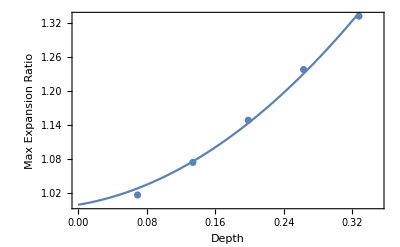

```mathematica
Show[ListPlot[maxpts,PlotRange->{{0,.35},Automatic},Frame->True,FrameLabel->{"Depth","Max Expansion Ratio"}],Plot[maxfit,{d,0,.35}]]
```

## Interpolation

### interpolation er(Log[c],d)

```mathematica
fitdataall=Table[{Log[data[i,"modulus"]],data[i,"d"],data[i,"expansion_ratio"]},{i,1,Length[data]}];
fitdataall=Join[fitdataall,Table[{Log[cs[[i]]],0,1},{i,1,Length[cs]}]];
```

```mathematica
erinterp=Interpolation[fitdataall,Method->"Spline"]
```

InterpolatingFunction[…]

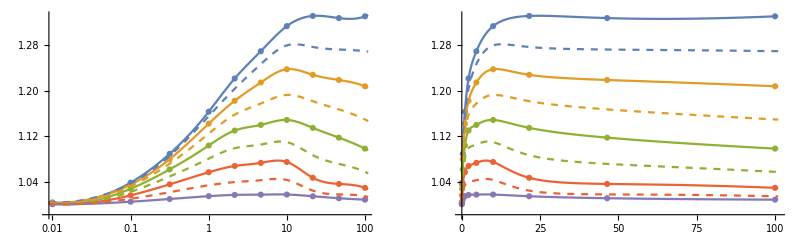

```mathematica
GraphicsGrid[
{{Show[ListLogLinearPlot[Table[Transpose[{data[Select[#d==ds[[i]] &],"modulus"],data[Select[#d==ds[[i]] &],"expansion_ratio"]}//Normal],{i,1,5}]
,PlotRange->{{.009,101},Automatic}],
LogLinearPlot[erinterp[Log[c],d]/.d->ds//Evaluate,{c,.009,110}],
LogLinearPlot[erinterp[Log[c],d]/.d->MovingAverage[ds,2]//Evaluate,{c,.009,110},PlotStyle->Dashed]],
Show[
ListPlot[Table[Transpose[{data[Select[#d==ds[[i]] &],"modulus"],data[Select[#d==ds[[i]] &],"expansion_ratio"]}//Normal],{i,1,5}]
,PlotRange->{{0,101},Automatic}],
Plot[erinterp[Log[c],d]/.d->ds//Evaluate,{c,.01,101}],
Plot[erinterp[Log[c],d]/.d->MovingAverage[ds,2]//Evaluate,{c,.01,101},PlotStyle->Dashed]
]}}
]
```

```mathematica
Show[Plot3D[erinterp[Log[c],d/3.6/1.5],{c,.01,100},{d,0,.35*1.5*3.6},AxesLabel->{"Bulkhead Modulus","Ablation Depth (μm)","Expansion Ratio"},PlotStyle->Opacity[.5],MaxRecursion->6,PlotPoints->50,LabelStyle->{FontSize->12,FontColor->Black}(*,PlotLegends->{"Interpolation"}*),ScalingFunctions->{"Log",Automatic,Automatic}],
ListPointPlot3D[Table[{data[i,"modulus"],data[i,"d"]*3.6*1.5,data[i,"expansion_ratio"]},{i,1,Length[data]}],ScalingFunctions->{"Log",Automatic,Automatic}(*,PlotLegends->{"Simulation"}*)]
]
```

-Graphics3D-

### interpolation d(Log[c],er)

```mathematica
fitdatad=Table[{{Log[data[i,"modulus"]],data[i,"expansion_ratio"]},data[i,"d"]},{i,1,Length[data]}];
fitdatad=Join[fitdatad,Table[{{Log[cs[[i]]],1},0},{i,1,Length[cs]}]];
```

```mathematica
dinterp=Interpolation[fitdatad,Method->"Spline"]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

InterpolatingFunction[…]

Fails because er isn’t on a grid, so can’t use higher order methods

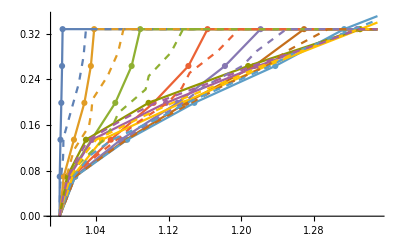

```mathematica
Show[
ListPlot[Table[Transpose[{data[Select[#modulus==cs[[i]] &],"expansion_ratio"],data[Select[#modulus==cs[[i]] &],"d"]}//Normal],{i,1,Length[cs]}]
,PlotRange->{{.99,1.35},{-.01,.35}}],
Plot[dinterp[Log[c],er]/.c->cs//Evaluate,{er,1,1.35}],
Plot[dinterp[Log[c],er]/.c->MovingAverage[cs,2]//Evaluate,{er,1,1.35},PlotStyle->Dashed]
]
```

```mathematica
Show[Plot3D[dinterp[Log[c],er],{c,.01,100},{er,1,1.35},AxesLabel->{"c","er","d"},PlotStyle->Opacity[.5],MaxRecursion->6,PlotPoints->50,ScalingFunctions->{"Log",Automatic,Automatic}],
ListPointPlot3D[Table[{data[i,"modulus"],data[i,"expansion_ratio"],data[i,"d"]},{i,1,Length[data]}],ScalingFunctions->{"Log",Automatic,Automatic}]
]
```

-Graphics3D-

### interpolation Log[c](d,er)

```mathematica
dataincreasing=data[Select[#modulus<=10&]];
fitdatac=Table[{dataincreasing[i,"d"],dataincreasing[i,"expansion_ratio"],Log[dataincreasing[i,"modulus"]]},{i,1,Length[dataincreasing]}];
```

```mathematica
cinterp=Interpolation[fitdatac]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[…]

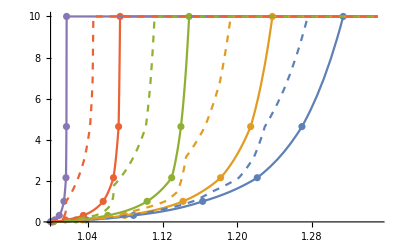

```mathematica
Show[
ListPlot[Table[Transpose[{dataincreasing[Select[#d==ds[[i]] &],"expansion_ratio"],dataincreasing[Select[#d==ds[[i]] &],"modulus"]}//Normal],{i,1,Length[ds]}]
,PlotRange->{{1,1.35},Automatic}],
Plot[Exp[cinterp[d,er]]/.d->ds//Evaluate,{er,1,1.35}],
Plot[Exp[cinterp[d,er]]/.d->MovingAverage[ds,2]//Evaluate,{er,1,1.35},PlotStyle->Dashed]
]
```

```mathematica
Show[Plot3D[Exp[cinterp[d,er]],{d,0,.325},{er,1,1.3},AxesLabel->{"d","er","c"},PlotStyle->Opacity[.5],MaxRecursion->6,PlotPoints->50],
ParametricPlot3D[{mind[er],er,Exp[cinterp[mind[er],er]]},{er,1,1.3}],
ListPointPlot3D[Table[{data[i,"d"],data[i,"expansion_ratio"],data[i,"modulus"]},{i,1,Length[data]}]]
]
```

-Graphics3D-

## Data on expansion ratios

Data from Maarten

```mathematica
erlistall={1.09760113,1.13251156,1.09609293,1.02211903,1,1.01796517,0.99746531,1.16196488,1.01156069,1.03853101,1.07427223,1.12765957,1.02261414,1.078125,0.99680284,1.07287449,0.99648073,1.25541619,1.09119497,1,1.10806595,1.06624331,1.01214575,1.1672326,1.00843289,1,1,1.02158682,1.16510388,1.05504587,1.01023556,1.05905512,1.09398496,1.17759197,1.06864942,1.15485733,1.09616246,1.00859599};
```

Ablations that Maarten deemed successful

```mathematica
erlist=Select[erlistall,#>1.04&];
```

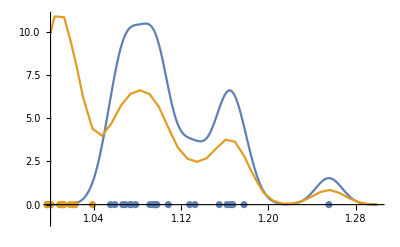

```mathematica
Show[Plot[{PDF[SmoothKernelDistribution[erlist,Automatic,{"Bounded",1,"Gaussian"}],er],PDF[SmoothKernelDistribution[erlistall,Automatic,{"Bounded",1,"Gaussian"}],er]},{er,1,1.3},PlotRange->{-1,Automatic}],
ListPlot[{Thread[{erlist,0}],Thread[{Select[erlistall,#<1.04&],0}]}]]
```

Exclude the 1.25 - geometry outside of SE model ability to describe

```mathematica
inferencedata=Select[erlist,#<1.2&]
```

{1.0976,1.13251,1.09609,1.16196,1.07427,1.12766,1.07813,1.07287,1.09119,1.10807,1.06624,1.16723,1.1651,1.05505,1.05906,1.09398,1.17759,1.06865,1.15486,1.09616}

## likelihood by sampling d

## Distribution of cut depths

### Minimum possible cut depth to observe er

```mathematica
dminsol=Solve[er==maxfiteq,d][[1]]
```

{d→(-z+√(-4 y+4 er y+z^2))/(2 y)}

```mathematica
mind[err_]:=d/.dminsol/.maxfitmod["BestFitParameters"]/.er->err
```

```mathematica
mind[er]
```

0.210654 (-0.250115+√(-9.43168+9.49424 er))

```mathematica
mind[1.1]
```

0.159225

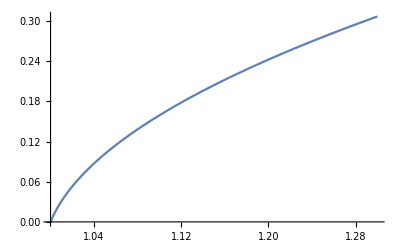

```mathematica
Plot[mind[er],{er,1,1.3}]
```

### distribution of cut depths

```mathematica
ddist=UniformDistribution[{mind[er],ds[[1]]}]
```

UniformDistribution[{0.210654 (-0.250115+√(-9.43168+9.49424 er)),0.327778}]

```mathematica
Manipulate[Plot[PDF[ddist,d]/.{er->err},{d,-.05,.35},AxesLabel->{"Cut Depth","PDF"}],{err,1,1.25}]
```

## Sample

```mathematica
getc[err_,dist_]:=Module[{dd},
dd=RandomVariate[dist/.er->err];
{FindRoot[err-erinterp[Log[c],dd],{c,Exp[cinterp[dd,err]],.01,100}],dd}
]
```

```mathematica
sam=getc[inferencedata[[1]],ddist]
```

{{c→0.943941},0.19342}

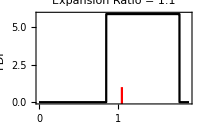

```mathematica
pdfdplot=Show[Plot[PDF[ddist,d/3.6/1.5]/.er->inferencedata[[1]],{d,0,.35*3.6*1.5},PlotStyle->Black,Frame->True,PlotLabel->"Expansion Ratio = "<>ToString[Round[inferencedata[[1]],.01]],FrameLabel->{"Ablation Depth (μm)","PDF"},LabelStyle->{FontSize->12,FontColor->Black}],
ListLinePlot[{{sam[[2]]*3.6*1.5,-1},{sam[[2]]*3.6*1.5,1}},PlotStyle->Red],
ImageSize->200]
```

```mathematica
Export["supps/pdf_d.pdf",pdfdplot]
```

supps/pdf_d.pdf

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
interp3dplot=Show[Plot3D[erinterp[Log[c],d/3.6/1.5],{c,.01,100},{d,0,.35*1.5*3.6},AxesLabel->{"Bulkhead Modulus","Ablation Depth (μm)","Expansion Ratio"},PlotStyle->Opacity[.5],MaxRecursion->6,PlotPoints->50,LabelStyle->{FontSize->12,FontColor->Black}(*,PlotLegends->{"Interpolation"}*),ScalingFunctions->{"Log",Automatic,Automatic},ViewPoint->Dynamic[vp]],
ListPointPlot3D[Table[{data[i,"modulus"],data[i,"d"]*3.6*1.5,data[i,"expansion_ratio"]},{i,1,Length[data]}],ScalingFunctions->{"Log",Automatic,Automatic}(*,PlotLegends->{"Simulation"}*)]
,ListLinePlot3D[{{.01,sam[[2]]*1.5*3.6,1.1},{100,sam[[2]]*1.5*3.6,1.1}},ScalingFunctions->{"Log",Automatic,Automatic},PlotStyle->{Red}]
,ListPointPlot3D[{{c/.sam[[1]],sam[[2]]*1.5*3.6,1.1}},ScalingFunctions->{"Log",Automatic,Automatic},PlotStyle->Red]
,ListLinePlot3D[{{{c/.sam[[1]],sam[[2]]*1.5*3.6,1.1},{c/.sam[[1]],sam[[2]]*1.5*3.6,1}},{{c/.sam[[1]],sam[[2]]*1.5*3.6,1},{c/.sam[[1]],0*1.5*3.6,1}}},ScalingFunctions->{"Log",Automatic,Automatic},PlotStyle->{{Red,Dashed}}]
]
```

-Graphics3D-

```mathematica
vp
```

{1.3,-2.4,2.}

```mathematica
goodvp={-2.3814188394700873,-1.9135354777929239,1.455069168886738}
```

{-2.38142,-1.91354,1.45507}

```mathematica
Export["supps/interp3d.pdf",Show[interp3dplot,{ViewPoint->goodvp},ImageSize->400],ImageResolution->500]
```

supps/interp3d.pdf

### Construct empirical distributions

#### CDFs from sampling d and finding c

```mathematica
csoutall=Table[Table[c/.getc[j,ddist][[1]],{i,1,1000}],{j,inferencedata}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
cdfall=CDF[EmpiricalDistribution[#]]&/@csoutall;
```

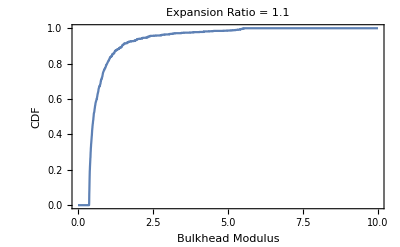

```mathematica
Plot[cdfall[[1]][c],{c,0,10},Frame->True,FrameLabel->{"Bulkhead Modulus","CDF"},PlotLabel->"Expansion Ratio = "<>ToString[Round[inferencedata[[1]],.1]],LabelStyle->{FontColor->Black,FontSize->12},PlotRange->All(*,PlotRange->{{1,1.5},{Automatic,.9}}*)]
```

#### PDF from fitting CDF and taking derivative

```mathematica
bzpdf[cvals_,cdf_]:=Module[{min,max,csample,cdfatcsample,bz},
min=Min[cvals];
max=Max[cvals];
csample=Exp@Range[Log@min,Log@max,Log[max/min]/200];
cdfatcsample=cdf/@csample;
bz=BezierFunction[Transpose[{csample,cdfatcsample}]];
{Piecewise[{{0,c<min},{0,c>max},{bz'[(Log[c]-Log[min])/(Log[max]-Log[min])][[2]],max>=c>=min}}],Piecewise[{{0,c<min},{1,c>max},{bz[(Log[c]-Log[min])/(Log[max]-Log[min])][[2]],max>=c>=min}}],
{csample,cdfatcsample}}
]
```

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.371588,0.001},{0.37664,0.072},{0.381762,0.107},«5»,{0.413987,0.267},{0.419617,0.29},«191»},{}},{1},MachinePrecision,Unevaluated][0.370198 «1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.371588,0.001},{0.37664,0.072},{0.381762,0.107},«5»,{0.413987,0.267},{0.419617,0.29},«191»},{}},{0},MachinePrecision,Unevaluated][0.370198 «1»] does not exist.

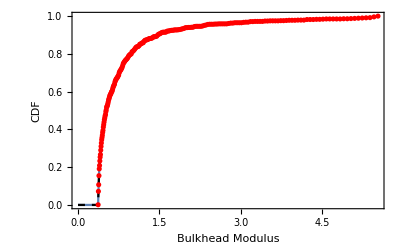

```mathematica
Show[Plot[cdfall[[1]][c],{c,0,3},PlotRange->All,PlotLegends->Placed[LineLegend[{"Empirical CDF"}],{Right,Bottom}],Frame->True,FrameLabel->{"Bulkhead Modulus","CDF"},LabelStyle->{FontSize->12,FontColor->Black}],
Plot[bzpdf[csoutall[[1]],cdfall[[1]]][[2]],{c,0,3},PlotRange->All,PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"Bezier Curve Fit"}],{Right,Bottom}]],
ListPlot[Transpose[bzpdf[csoutall[[1]],cdfall[[1]]][[3]]],PlotStyle->Red]]
```

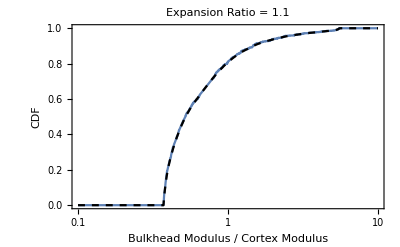

```mathematica
cdfwfitplot=Show[LogLinearPlot[cdfall[[1]][c],{c,.1,10},PlotRange->All,PlotLegends->Placed[LineLegend[{"Empirical CDF"}],{Right,Bottom}],Frame->True,FrameLabel->{"Bulkhead Modulus / Cortex Modulus","CDF"},LabelStyle->{FontSize->12,FontColor->Black},PlotLabel->"Expansion Ratio = "<>ToString[Round[inferencedata[[1]],.1]]],
LogLinearPlot[bzpdf[csoutall[[1]],cdfall[[1]]][[2]],{c,.1,10},PlotRange->All,PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"Bezier Curve Fit"}],{Right,Bottom}]]
]
```

```mathematica
Export["supps/cdfwfit.pdf",Show[cdfwfitplot,ImageSize->300]]
```

supps/cdfwfit.pdf

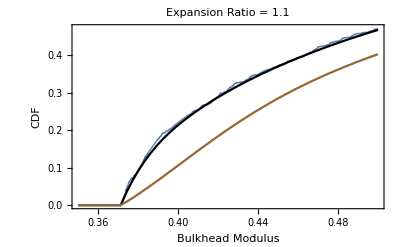

```mathematica
cdfwfitzoom=Show[Plot[cdfall[[1]][c],{c,.35,.5},PlotRange->All,PlotLegends->Placed[LineLegend[{"Empirical CDF"}],{Right,Bottom}],Frame->True,FrameLabel->{"Bulkhead Modulus","CDF"},LabelStyle->{FontSize->12,FontColor->Black},PlotStyle->Thick,PlotLabel->"Expansion Ratio = "<>ToString[Round[inferencedata[[1]],.1]]],
Plot[bzpdf[csoutall[[1]],cdfall[[1]]][[2]],{c,.35,.5},PlotRange->All,PlotStyle->{Black,Medium},PlotLegends->Placed[LineLegend[{"Bezier Curve Fit"}],{Right,Bottom}]],
Plot[CDF[SmoothKernelDistribution[csoutall[[1]],Automatic,{"Bounded",Min[csoutall[[1]]],"Gaussian"}],c],{c,.35,.5},PlotLegends->Placed[LineLegend[{"Kernel Density"}],{Right,Bottom}],PlotStyle->{Brown}]
]
```

```mathematica
Export["supps/cdfwfitzoom.pdf",Show[cdfwfitzoom,ImageSize->300]]
```

supps/cdfwfitzoom.pdf

```mathematica
pdfall=Table[bzpdf[csoutall[[i]],cdfall[[i]]][[1]],{i,1,Length[csoutall]}];
```

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.371588,0.001},{0.37664,0.072},{0.381762,0.107},«5»,{0.413987,0.267},{0.419617,0.29},«191»},{}},{1},MachinePrecision,Unevaluated][0.370198 «1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.371588,0.001},{0.37664,0.072},{0.381762,0.107},«5»,{0.413987,0.267},{0.419617,0.29},«191»},{}},{0},MachinePrecision,Unevaluated][0.370198 «1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.65634,0.001},{0.663541,0.053},{0.670821,0.102},«5»,{0.716209,0.276},{0.724066,0.29},«191»},{}},{1},MachinePrecision,Unevaluated][0.45823 («1»)] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

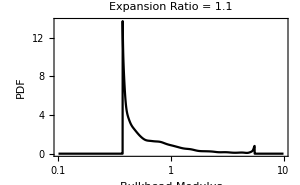

```mathematica
pdfcplot=LogLinearPlot[pdfall[[1]],{c,.1,10},PlotRange->{{.1,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","PDF"},PlotStyle->Black,LabelStyle->{FontColor->Black,FontSize->12},PlotLabel->"Expansion Ratio = "<>ToString[Round[inferencedata[[1]],.1]],ImageSize->300]
```

```mathematica
Export["supps/pdf_c.pdf",pdfcplot]
```

supps/pdf_c.pdf

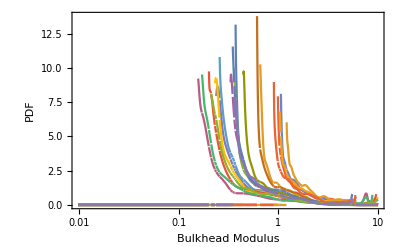

```mathematica
LogLinearPlot[pdfall,{c,0,10},PlotRange->{{.5,All},{0,15}},Frame->True,FrameLabel->{"Bulkhead Modulus","PDF"},LabelStyle->{FontColor->Black,FontSize->12},PlotLegends->Placed[LineLegend[{"","","","",""},LegendLabel->"Measured expansion ratios",Spacings->0],{Right,Top}]]
```

### Construct likelihoods

```mathematica
likeall=Times@@pdfall;
```

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.371588,0.001},{0.37664,0.072},{0.381762,0.107},«5»,{0.413987,0.267},{0.419617,0.29},«191»},{}},{1},MachinePrecision,Unevaluated][0.370198 «1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.65634,0.001},{0.663541,0.053},{0.670821,0.102},«5»,{0.716209,0.276},{0.724066,0.29},«191»},{}},{1},MachinePrecision,Unevaluated][0.45823 («1»)] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{«1»,{}},{1},MachinePrecision,Unevaluated][0.364983 (1.01735+Log[c])] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

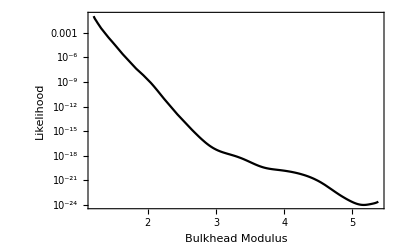

```mathematica
LogPlot[likeall,{c,0,10},PlotRange->{{0,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","Likelihood"},PlotStyle->Black,LabelStyle->{FontColor->Black,FontSize->12}]
```

### Assuming different distributions of d

```mathematica
stdmin=.25/3.6/1.5
```

0.0462963

#### Exponential

```mathematica
ddistexp=TruncatedDistribution[{mind[er],ds[[1]]},ExponentialDistribution[1/stdmin]]
```

TruncatedDistribution[{0.210654 (-0.250115+√(-9.43168+9.49424 er)),0.327778},ExponentialDistribution[21.6]]

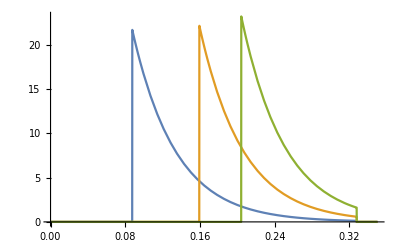

```mathematica
Plot[{PDF[ddistexp,d]/.er->1.04,PDF[ddistexp,d]/.er->1.1,PDF[ddistexp,d]/.er->1.15},{d,0,.35},PlotRange->All]
```

```mathematica
getc[1.1,ddistexp]
```

{{c→1.18311},0.185178}

```mathematica
csoutallexp=Table[Table[c/.getc[j,ddistexp][[1]],{i,1,1000}],{j,inferencedata}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
cdfallexp=CDF[EmpiricalDistribution[#]]&/@csoutallexp;
```

```mathematica
pdfallexp=Table[bzpdf[csoutallexp[[i]],cdfallexp[[i]]][[1]],{i,1,Length[csoutallexp]}];
```

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.372046,0.001},{0.377131,0.006},{0.382287,0.013},«5»,{0.414731,0.039},{0.4204,0.041},«191»},{}},{1},MachinePrecision,Unevaluated][0.368277 («19»+«1»)] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.372046,0.001},{0.377131,0.006},{0.382287,0.013},«5»,{0.414731,0.039},{0.4204,0.041},«191»},{}},{0},MachinePrecision,Unevaluated][0.368277 («19»+«1»)] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.65664,0.001},{0.663836,0.012},{0.671111,0.019},«5»,{0.716469,0.069},{0.724321,0.075},«191»},{}},{1},MachinePrecision,Unevaluated][0.45872 («1»)] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

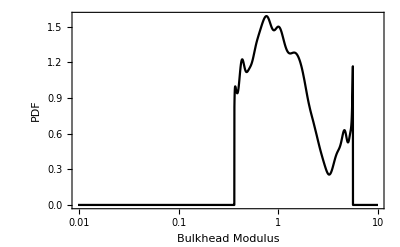

```mathematica
LogLinearPlot[pdfallexp[[3]],{c,0,10},PlotRange->{{.1,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","PDF"},PlotStyle->Black,LabelStyle->{FontColor->Black,FontSize->12}]
```

```mathematica
likeallexp=Times@@pdfallexp;
```

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.372046,0.001},{0.377131,0.006},{0.382287,0.013},«5»,{0.414731,0.039},{0.4204,0.041},«191»},{}},{1},MachinePrecision,Unevaluated][0.368277 («19»+«1»)] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.65664,0.001},{0.663836,0.012},{0.671111,0.019},«5»,{0.716469,0.069},{0.724321,0.075},«191»},{}},{1},MachinePrecision,Unevaluated][0.45872 («1»)] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.362103,0.001},{0.367098,0.005},{0.372163,0.011},«5»,{0.40405,0.039},{0.409624,0.042},«191»},{}},{1},MachinePrecision,Unevaluated][0.364931 («19»+Log[c])] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

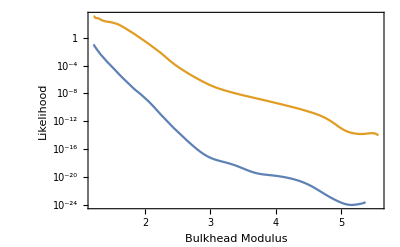

```mathematica
LogPlot[{likeall,likeallexp},{c,0,10},PlotRange->{{0,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","Likelihood"},LabelStyle->{FontColor->Black,FontSize->12}]
```

#### Half normal

```mathematica
ddistnorm=TruncatedDistribution[{mind[er],ds[[1]]},NormalDistribution[mind[er],stdmin]]
```

TruncatedDistribution[{0.210654 (-0.250115+√(-9.43168+9.49424 er)),0.327778},NormalDistribution[0.210654 (-0.250115+√(-9.43168+9.49424 er)),0.0462963]]

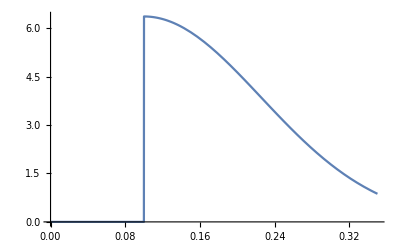

```mathematica
Plot[PDF[HalfNormalDistribution[1/.1],x-.1],{x,0,.35},PlotRange->All]
```

CompiledFunction::cfsa: Argument 0.210654 (-0.250115+√(-9.43168+9.49424 er)) at position 2 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

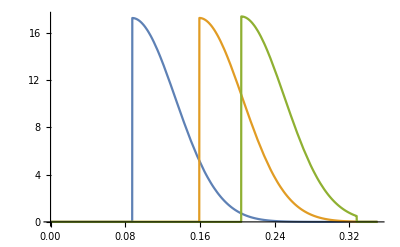

```mathematica
Plot[{PDF[ddistnorm,d]/.er->1.04,PDF[ddistnorm,d]/.er->1.1,PDF[ddistnorm,d]/.er->1.15},{d,0,.35},PlotRange->All]
```

```mathematica
csoutallnorm=Table[Table[c/.getc[j,ddistnorm][[1]],{i,1,1000}],{j,inferencedata}];
cdfallnorm=CDF[EmpiricalDistribution[#]]&/@csoutallnorm;
pdfallnorm=Table[bzpdf[csoutallnorm[[i]],cdfallnorm[[i]]][[1]],{i,1,Length[csoutallnorm]}];
likeallnorm=Times@@pdfallnorm;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.400354,0.001},{0.405653,0.001},{0.411021,0.003},{0.416461,0.004},«3»,{0.43895,0.008},{0.44476,0.008},{0.450646,0.012},«191»},{}},{1},MachinePrecision,Unevaluated][«1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.400354,0.001},{0.405653,0.001},{0.411021,0.003},{0.416461,0.004},«3»,{0.43895,0.008},{0.44476,0.008},{0.450646,0.012},«191»},{}},{0},MachinePrecision,Unevaluated][«1»] does not exist.

Part::partw: Part 2 of BezierFunction[1,{{0.,1.}},{200},{{{0.661759,0.001},{0.668935,0.004},{0.676189,0.007},«5»,{0.721394,0.043},{0.729216,0.044},«191»},{}},{1},MachinePrecision,Unevaluated][0.463588 («1»)] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

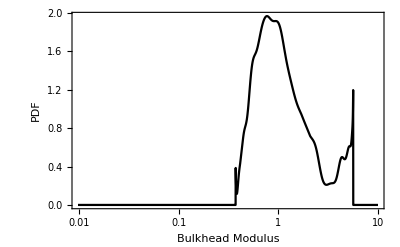

```mathematica
LogLinearPlot[pdfallnorm[[3]],{c,0,10},PlotRange->{{.1,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","PDF"},PlotStyle->Black,LabelStyle->{FontColor->Black,FontSize->12}]
```

#### All together

CompiledFunction::cfsa: Argument 0.210654 (-0.250115+√(-9.43168+9.49424 er)) at position 2 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

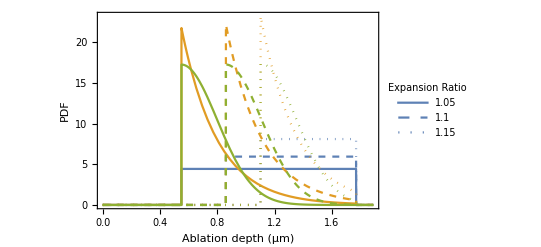

```mathematica
multdists=Plot[{PDF[ddist,d/1.5/3.6]/.er->1.05,PDF[ddist,d/1.5/3.6]/.er->1.1,PDF[ddist,d/1.5/3.6]/.er->1.15,
PDF[ddistexp,d/1.5/3.6]/.er->1.05,PDF[ddistexp,d/1.5/3.6]/.er->1.1,PDF[ddistexp,d/1.5/3.6]/.er->1.15,
PDF[ddistnorm,d/1.5/3.6]/.er->1.05,PDF[ddistnorm,d/1.5/3.6]/.er->1.1,PDF[ddistnorm,d/1.5/3.6]/.er->1.15},{d,0,.35*1.5*3.6},PlotRange->All,PlotStyle->{{ColorData[97,"ColorList"][[1]]},{ColorData[97,"ColorList"][[1]],Dashed},{ColorData[97,"ColorList"][[1]],Dotted},
{ColorData[97,"ColorList"][[2]]},{ColorData[97,"ColorList"][[2]],Dashed},{ColorData[97,"ColorList"][[2]],Dotted},
{ColorData[97,"ColorList"][[3]]},{ColorData[97,"ColorList"][[3]],Dashed},{ColorData[97,"ColorList"][[3]],Dotted}},
PlotLegends->LineLegend[{"1.05","1.1","1.15"},LegendLabel->"Expansion Ratio"],
Frame->True,FrameLabel->{"Ablation depth (μm)","PDF"},
LabelStyle->{FontColor->Black,FontSize->12}
]
```

```mathematica
Export["supps/multdists.pdf",multdists,ImageSize->250]
```

supps/multdists.pdf

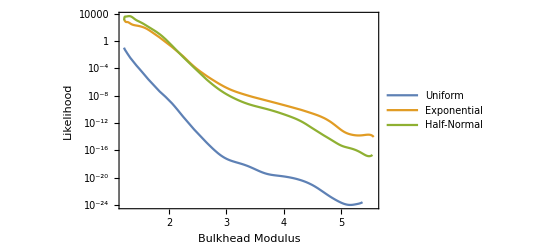

```mathematica
multlikes=LogPlot[{likeall,likeallexp,likeallnorm},{c,0,10},PlotRange->{{0,All},All},Frame->True,FrameLabel->{"Bulkhead Modulus","Likelihood"},LabelStyle->{FontColor->Black,FontSize->12},PlotLegends->Placed[LineLegend[{"Uniform","Exponential","Half-Normal"}],Left]]
```

```mathematica
Export["supps/multlikes.pdf",multlikes,ImageSize->250]
```

supps/multlikes.pdf

## Main text figure

```mathematica
maxerofc=1+((-a+c)^2 y)/b^2+((-a+c) z)/b
```

1+((-a+c)^2 y)/b^2+((-a+c) z)/b

```mathematica
cmaxfit={a->2.544460271897277,b->46.76112006148753}
```

{a→2.54446,b→46.7611}

```mathematica
maxcofer=Solve[er==maxerofc,c][[2]]
```

{c→(2 a y-b z+b √(-4 y+4 er y+z^2))/(2 y)}

```mathematica
csdmin=Table[(c/.maxcofer)/.maxfitmod["BestFitParameters"]/.cmaxfit/.er->inferencedata[[i]],{i,1,Length[inferencedata]}]
(*csdmin=Exp[cinterp[mind[er],er]]/.er->inferencedata
```

{9.87784,11.4008,9.80667,12.5418,8.7116,11.2016,8.91483,8.63668,9.57187,10.3581,8.27191,12.735,12.6573,7.61598,7.8572,9.70632,13.1066,8.40612,12.2762,9.80996}

```mathematica
csdmax=Exp[cinterp[ds[[1]],er]]/.er->inferencedata
```

{0.362519,0.623841,0.354117,0.986203,0.227446,0.578508,0.248218,0.220348,0.32815,0.426578,0.189576,1.05898,1.02986,0.147053,0.161053,0.342698,1.21293,0.20021,0.88302,0.3545}

```mathematica
rangelines=Table[{{csdmin[[i]],.95-.15*i/Length[csdmax]},{csdmax[[i]],.95-.15*i/Length[csdmax]}},{i,1,Length[csdmax]}]
```

{{{9.87784,0.9425},{0.362519,0.9425}},{{11.4008,0.935},{0.623841,0.935}},{{9.80667,0.9275},{0.354117,0.9275}},{{12.5418,0.92},{0.986203,0.92}},{{8.7116,0.9125},{0.227446,0.9125}},{{11.2016,0.905},{0.578508,0.905}},{{8.91483,0.8975},{0.248218,0.8975}},{{8.63668,0.89},{0.220348,0.89}},{{9.57187,0.8825},{0.32815,0.8825}},{{10.3581,0.875},{0.426578,0.875}},{{8.27191,0.8675},{0.189576,0.8675}},{{12.735,0.86},{1.05898,0.86}},{{12.6573,0.8525},{1.02986,0.8525}},{{7.61598,0.845},{0.147053,0.845}},{{7.8572,0.8375},{0.161053,0.8375}},{{9.70632,0.83},{0.342698,0.83}},{{13.1066,0.8225},{1.21293,0.8225}},{{8.40612,0.815},{0.20021,0.815}},{{12.2762,0.8075},{0.88302,0.8075}},{{9.80996,0.8},{0.3545,0.8}}}

```mathematica
erpoints=Table[{{.002+.001*RandomReal[{-.5,.5}],inferencedata[[i]]}},{i,1,Length[inferencedata]}]
```

{{{0.00226952,1.0976}},{{0.00163997,1.13251}},{{0.00236156,1.09609}},{{0.00220015,1.16196}},{{0.00243916,1.07427}},{{0.00187423,1.12766}},{{0.00243847,1.07813}},{{0.00179177,1.07287}},{{0.00226178,1.09119}},{{0.00202431,1.10807}},{{0.00244649,1.06624}},{{0.00226843,1.16723}},{{0.00196145,1.1651}},{{0.00191358,1.05505}},{{0.00179433,1.05906}},{{0.00172655,1.09398}},{{0.00218303,1.17759}},{{0.00246036,1.06865}},{{0.00200015,1.15486}},{{0.00160125,1.09616}}}

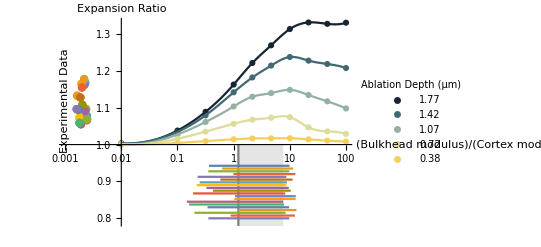

```mathematica
scl=500/360;
erfig=Show[ListLogLinearPlot[Table[Transpose[{data[Select[#d==ds[[i]] &],"modulus"],data[Select[#d==ds[[i]] &],"expansion_ratio"]}//Normal],{i,1,5}],PlotRange->{{.001,Automatic},{.79,Automatic}},AxesOrigin->{.01,1},AxesLabel->{("Bulkhead modulus")/("Cortex modulus"),"Expansion Ratio"},LabelStyle->{FontSize->10*scl,FontColor->Black,FontFamily->"Arial"},PlotStyle->"StarryNightColors",
PlotRangeClipping->False,
AxesStyle->AbsoluteThickness[1.02],PlotLegends->Placed[LineLegend[Round[ds*3.6*1.5,.01],LegendLabel->"Ablation Depth (μm)",LabelStyle->{FontSize->8*scl,FontFamily->"Arial"},Spacings->0],Scaled[{1,.85}]],
ImageSize->275*scl,Epilog->{Inset[Rotate[Text[Style["Experimental Data",8*scl]],90 Degree],{-6.9,1.12}],Text[Style["Moduli consistent
with data points",8*scl,TextAlignment->Left,FontFamily->"Arial"],{4.9,.81}]}],
LogLinearPlot[erinterp[Log[c],d]/.d->ds//Evaluate,{c,.01,100},PlotStyle->"StarryNightColors"],
LogLinearPlot[.7,{c,1.212928192904417,Min[csdmin]},PlotStyle->Gray,Filling->1],
Legended[ListLinePlot[{{1.212928192904417,.7},{1.212928192904417,1}},ScalingFunctions->{"Log"},PlotStyle->Gray],Placed[Rotate[LineLegend[{Gray},{"Most likely
modulus"},LabelStyle->FontSize->8*scl],90Degree],Scaled[{.35,.15}]]],
ListLinePlot[rangelines,ScalingFunctions->{"Log"}],
ListPlot[erpoints,ScalingFunctions->{"Log"},PlotStyle->PointSize->.015]
]
```

```mathematica
Export["erfig.pdf",erfig]
```

erfig.pdf